```mathematica
Integrate[k λ / (Sqrt[(x-x0)^2+(b-y0)^2]),{x,a,a+l}]
```

$Aborted

```mathematica
EFL[x0_,y0_,a_,b_,l_] :=(*0.0001 (Log[a+l-x0+√((a+l-x0)^2+(b-y0)^2)]-Log[a-x0+√(a^2+b^2-2 a x0+x0^2-2 b y0+y0^2)])*) Integrate[k λ / (Sqrt[(x-x0)^2+(b-y0)^2]),{x,a,a+l}]
EFD[x0_,y0_,a_,b_]:=k*λ*L/(*EuclideanDistance[{x0,y0},{a,b}]*)Sqrt[(x0-a)^2 + (y0-b)^2]
```

```mathematica
?EFL
```

Global`EFL

EFL[x0_,y0_,a_,b_,l_]:=0.0001 (Log[a+l-x0+√((a+l-x0)^2+(b-y0)^2)]-Log[a-x0+√(a^2+b^2-2 a x0+x0^2-2 b y0+y0^2)])

```mathematica
k = 0.0001;
λ = 1;
L= 10;
x1 = 0;
y1 = 0;
a=.
b=.
```

```mathematica
Plot3D[EFL[x0,y0,x1,y1,L],{x0,-5,15},{y0,-10,10},PlotPoints->100,MeshFunctions->{#3&},Mesh->5]
```

-Graphics3D-

```mathematica
Plot3D[EFL[x0,y0,x1,y1,L]-EFL[x0,y0,x1,y1+19,L],{x0,-5.5,15.5},{y0,-2,21},PlotPoints->120,MeshFunctions->{#3&},Mesh->20]
```

-Graphics3D-

{0.0001 ((-1-(10-x0)/(√((10-x0)^2+(19-y0)^2)))/(10-x0+√((10-x0)^2+(19-y0)^2))-(-1+x0/(√(361+x0^2-38 y0+y0^2)))/(-x0+√(361+x0^2-38 y0+y0^2)))-0.0001 ((-1-(10-x0)/(√((10-x0)^2+(0.5-y0)^2)))/(10-x0+√((10-x0)^2+(0.5-y0)^2))-(-1+x0/(√(0.25+x0^2-1. y0+y0^2)))/(-x0+√(0.25+x0^2-1. y0+y0^2))),0.0001 (-(19-y0)/((10-x0+√((10-x0)^2+(19-y0)^2)) √((10-x0)^2+(19-y0)^2))-(-38+2 y0)/(2 √(361+x0^2-38 y0+y0^2) (-x0+√(361+x0^2-38 y0+y0^2))))-0.0001 (-(0.5-y0)/((10-x0+√((10-x0)^2+(0.5-y0)^2)) √((10-x0)^2+(0.5-y0)^2))-(-1.+2 y0)/(2 √(0.25+x0^2-1. y0+y0^2) (-x0+√(0.25+x0^2-1. y0+y0^2))))}

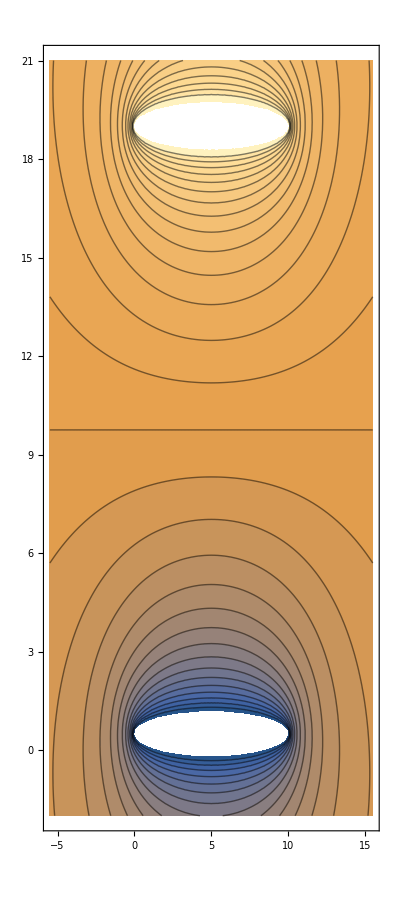

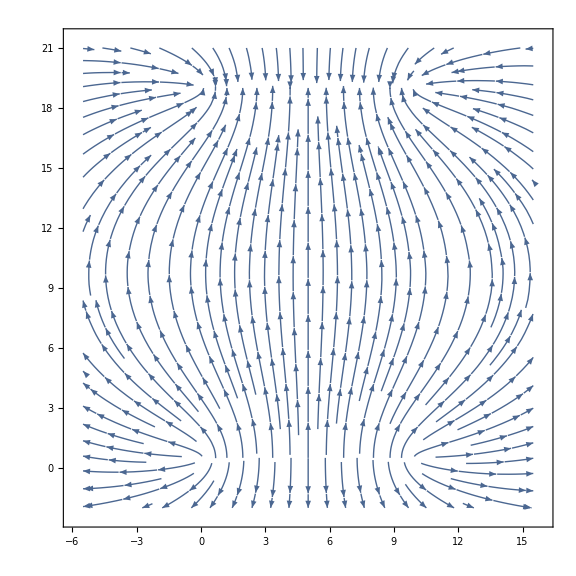

```mathematica
Grad[ -EFL[x0,y0,x1,y1+0.5,L]+EFL[x0,y0,x1,y1+19,L],{x0,y0}]

ContourPlot[-EFL[x0,y0,x1,y1+0.5,L]+EFL[x0,y0,x1,y1+19,L],{x0,-5.5,15.5},{y0,-2,21},PlotPoints->50,Contours->30, Axes->False,Frame->True]
StreamPlot[%%,{x0,-5.5,15.5},{y0,-2,21},StreamStyle-> Default,StreamPoints->Fine,Axes->False,Frame->True]
```

```mathematica
Plot3D[EFL[x0,y0,x1,y1,L]-EFD[x0,y0,5,19],{x0,-5.5,15.5},{y0,-2,21},PlotPoints->100]
ContourPlot[EFL[x0,y0,x1,y1+0.5,L]-EFD[x0,y0,5,19],{x0,-5.5,15.5},{y0,-2,21},PlotPoints->100,Contours->30]
```

-Graphics3D-

-Graphics-

{-(0.001 (-5+x0))/(((-5+x0)^2+(-19.5+y0)^2)^(3/2))-0.0001 ((-1-(10-x0)/(√((10-x0)^2+(0.5-y0)^2)))/(10-x0+√((10-x0)^2+(0.5-y0)^2))-(-1+x0/(√(0.25+x0^2-1. y0+y0^2)))/(-x0+√(0.25+x0^2-1. y0+y0^2))),-(0.001 (-19.5+y0))/(((-5+x0)^2+(-19.5+y0)^2)^(3/2))-0.0001 (-(0.5-y0)/((10-x0+√((10-x0)^2+(0.5-y0)^2)) √((10-x0)^2+(0.5-y0)^2))-(-1.+2 y0)/(2 √(0.25+x0^2-1. y0+y0^2) (-x0+√(0.25+x0^2-1. y0+y0^2))))}

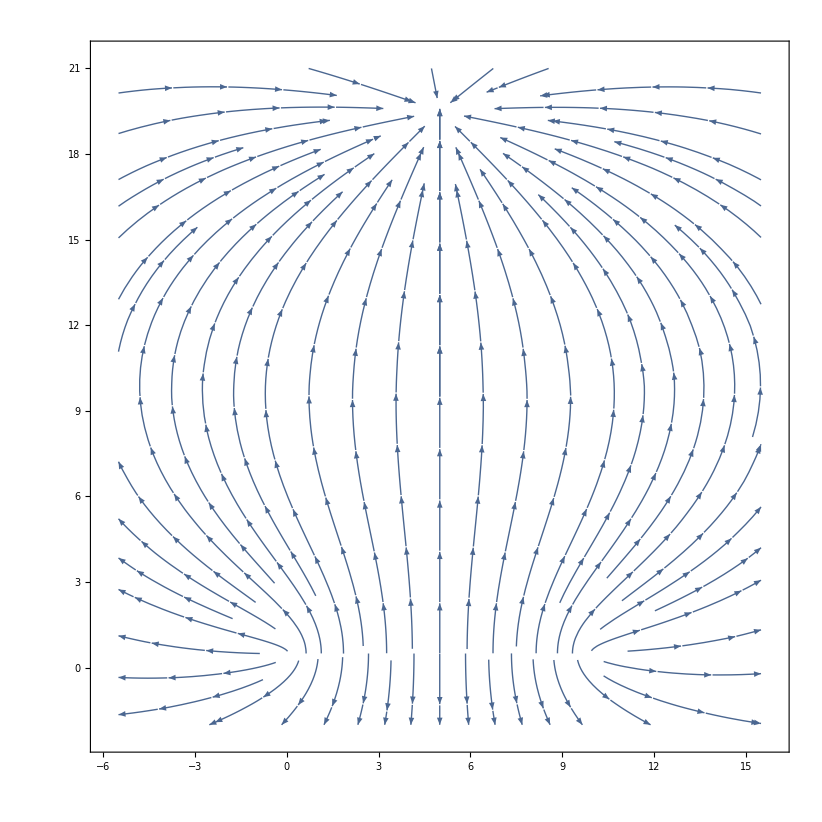

{-0.0001 ((-1-(10-x0)/(√((10-x0)^2+y0^2)))/(10-x0+√((10-x0)^2+y0^2))-(-1+x0/(√(x0^2+y0^2)))/(-x0+√(x0^2+y0^2))),-0.0001 (y0/(√((10-x0)^2+y0^2) (10-x0+√((10-x0)^2+y0^2)))-y0/(√(x0^2+y0^2) (-x0+√(x0^2+y0^2))))}

```mathematica
Grad[-EFL[x0,y0,x1,y1+0.5,L]+EFD[x0,y0,5,19.5],{x0,y0}]
StreamPlot[%, {x0,-5.5,15.5},{y0,-2,21}]
Grad[-EFL[x0,y0,x1,y1,L],{x0,y0}]
StreamPlot[ %,{x0,-5.5,15.5},{y0,-2,21}]
Grad[EFD[x0,y0,5,19.5],{x0,y0}]
StreamPlot[%, {x0,-5.5,15.5},{y0,-2,21}]
```

```mathematica
L1 = 100

Plot3D[EFL[x0,y0,x1-40,y1,L1]-EFL[x0,y0,x1-40,y1+19,L1],{x0,-5.5,15.5},{y0,-2,21},PlotPoints->120,MeshFunctions->{#3&},Mesh->20]
```

100

-Graphics3D-

{(0.001 x0)/((x0^2+(-10+y0)^2)^(3/2))-(0.001 x0)/((x0^2+y0^2)^(3/2)),(0.001 (-10+y0))/((x0^2+(-10+y0)^2)^(3/2))-(0.001 y0)/((x0^2+y0^2)^(3/2))}

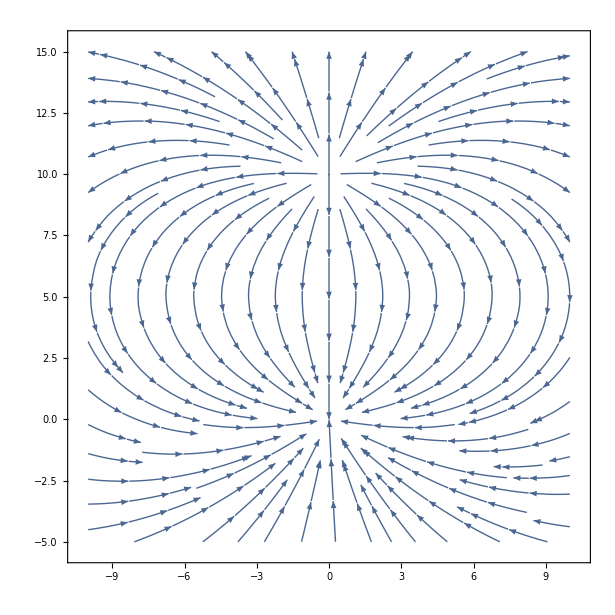

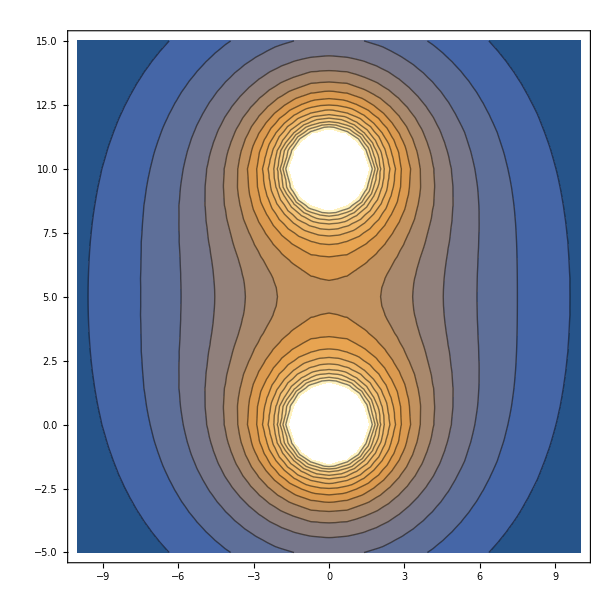

```mathematica
Grad[EFD[x0,y0,0,0]-EFD[x0,y0,0,10],{x0,y0}]
StreamPlot[%,{x0,+10,-10},{y0,-5,15}]
ContourPlot[EFD[x0,y0,0,0]+EFD[x0,y0,0,10],{x0,+10,-10},{y0,-5,15},Contours->15]
```